# Self-energy contribution to partonic neutralino pair production

Renormalisation of wave functions in partonic neutralino pair production to NLO.

## Initialisation

Load FeynCalc and FeynArts. Furthermore, this notebook makes use of three packages found in the “include” folder.

```mathematica
description = "Self-energy contribution to cross section of neutralino pair production at parton level.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts", "FeynHelpers"};
<<FeynCalc`
$FAVerbose = 0;

FCCheckVersion[9,3,1];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
$EwinoRoot = ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$EwinoRoot, "include"}]];
<< XSec`
<< EWinos`
<< CalcTools`
```

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

```mathematica
ResultsDir = FileNameJoin[{$EwinoRoot, "results", "NLO"}];
LOResultsDir = FileNameJoin[{$EwinoRoot, "results", "LO"}];
```

Set options to keep scaleless loop integrals and set Mandelstam parameters.

```mathematica
$KeepLogDivergentScalelessIntegrals = True;
SetMandelstamParameters[s, t, u, Power[MNeu[i],2] + Power[MNeu[j], 2]];
FAPatch[PatchModelsOnly->True];
```

Successfully patched FeynArts.

## Generate Feynman diagrams

Some text

```mathematica
ExcludedParticles = {
	V[1], (*photon*)
	V[2], (*Z boson*)
	V[3], (*W boson*)
	F[11], (*neutralinos*)
	F[12], (*charginos*)
	S[1], (*light higgs*)
	S[2], (*heavy higgs*)
	S[3], (*pseudoscalar higgs*)
	S[4], (*G0*)
	S[5], (*charged higgs*)
	S[6], (*charged G*)
	S[11], (*sneutrinos*)
	S[12], (*sleptons*)
(*	F[15], (*gluinos*)
	S[13], (*up squarks*)
	S[14], (*down squarks*)*)
	F[1], (*neutrinos*)
	F[2] (*leptons*)
};
ExcludedCouplings = {
(*	FieldPoint[_][F[3],S[13],F[11]],
	FieldPoint[_][V[1],V[2],S[1]],
	FieldPoint[_][V[1],V[2],S[2]],
	FieldPoint[_][V[1],V[2],S[3]],
	FieldPoint[_][V[1],V[2],S[4]],
	FieldPoint[_][V[1],V[2],S[12]]*)
};
parameters = {
	InsertionLevel->{Classes},
	Model->MSSMQCD,
	Restrictions->{NoLightFHCoupling, NoElectronHCoupling},
	ExcludeParticles->ExcludedParticles
};
parametersCT = {
	InsertionLevel->{Classes},
	Model->SMQCD,
	Restrictions->{NoLightFHCoupling, NoElectronHCoupling},
	ExcludeParticles->ExcludedParticles
};

SETopology[order_] := CreateTopologies[order, 1->1, ExcludeTopologies -> {Tadpoles, WFCorrections, WFCorrectionCTs}];
SETopologyCT[order_] := CreateCTTopologies[order, 1->1, ExcludeTopologies -> {Tadpoles, WFCorrections, WFCorrectionCTs}];

TriTopology[order_] := CreateTopologies[order, 2->1, ExcludeTopologies -> {Tadpoles, WFCorrections, WFCorrectionCTs, SelfEnergies}];
TriTopologyCT[order_] := CreateCTTopologies[order, 2->1, ExcludeTopologies -> {Tadpoles, WFCorrections, WFCorrectionCTs, SelfEnergyCTs}];
```

```mathematica
diagQuarkSE[order_] := InsertFields[SETopology[order], {F[3, {1}]} ->{F[3, {1}]}, Sequence@@parameters];
diagQuarkSECT[order_] := InsertFields[SETopologyCT[order], {F[3, {1}]} ->{F[3, {1}]}, Sequence@@parametersCT];

diagQuarkZVertex[order_] := InsertFields[TriTopology[order], {F[3, {1}], -F[3, {1}]} ->{V[2]}, Sequence@@parameters];
diagQuarkZVertexCT[order_] := InsertFields[TriTopologyCT[order], {F[3, {1}], -F[3, {1}]} ->{V[2]}, Sequence@@parametersCT];

diagZSE[order_] := InsertFields[SETopology[order], {V[2]} -> {V[2]}, Sequence@@parameters];
diagZSECT[order_] := InsertFields[SETopologyCT[order], {V[2]} -> {V[2]}, Sequence@@parametersCT];

diagGlSE[order_] := InsertFields[SETopology[order], {V[5]} -> {V[5]}, Sequence@@parameters];
diagGlSECT[order_] := InsertFields[SETopologyCT[order], {V[5]} -> {V[5]}, Sequence@@parametersCT];

diagGluinoSE[order_] := InsertFields[SETopology[order], {F[15]} -> {F[15]}, Sequence@@parameters];
(*diagGluinoSECT[order_] := InsertFields[SETopologyCT[order], {V[5]} -> {V[5]}, Sequence@@parametersCT];*)

(*
{diagSquarkSE, diagSquarkSECT} = InsertFields[#, {S[13, {A, g, a}]} ->{S[13, {A, g, a}]}, Sequence@@parameters] &/@ {SETopology, SETopologyCT};
{diagQuarkZVertex, diagQuarkZVertexCT} = InsertFields[#, {F[3, {g, a}], -F[3, {g, b}]} ->{V[2]}, Sequence@@parameters] &/@ {TriTopology, TriTopologyCT};
{diagQuarkSquarkNeutralinoVertex, diagQuarkSquarkNeutralinoVertexCT} = InsertFields[#, {F[3, {g, a}], -S[13, {A, g, b}]} ->{F[11, {i}]}, Sequence@@parameters] &/@ {TriTopology, TriTopologyCT};*)
```

```mathematica
diag1[0] = diagQuarkSE[1][[0]][Sequence@@diagQuarkSE[1], Sequence@@diagQuarkSECT[1]];
diag2[0] = diagZSE[1][[0]][Sequence@@diagZSE[1], Sequence@@diagZSECT[1]];
(*diag2[0] = diagSquarkSE[[0]][Sequence@@diagSquarkSE, Sequence@@diagSquarkSECT];*)
diag3[0] = diagQuarkZVertex[1][[0]][Sequence@@diagQuarkZVertex[1], Sequence@@diagQuarkZVertexCT[1]];
(*diag4[0] = diagQuarkSquarkNeutralinoVertex[[0]][Sequence@@diagQuarkSquarkNeutralinoVertex, Sequence@@diagQuarkSquarkNeutralinoVertexCT];*)
diag4[0] = diagGlSE[1][[0]][Sequence@@diagGlSE[1], Sequence@@diagGlSECT[1]];
diag5[0] = diagGluinoSE[1][[0]][Sequence@@diagGluinoSE[1]];
```

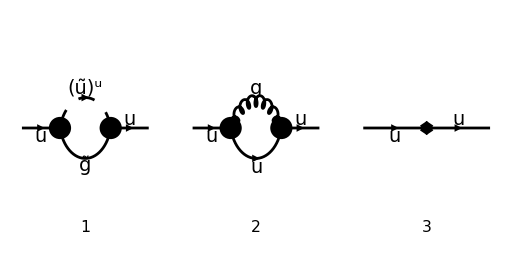

```mathematica
Paint[diag1[0], ColumnsXRows -> {3, 1}, Numbering -> Simple, ImageSize -> {512, 256}];
```

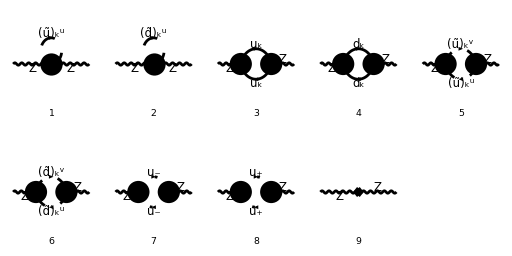

```mathematica
Paint[diag2[0], ColumnsXRows -> {5, 2}, Numbering -> Simple, ImageSize -> {512, 256}];
```

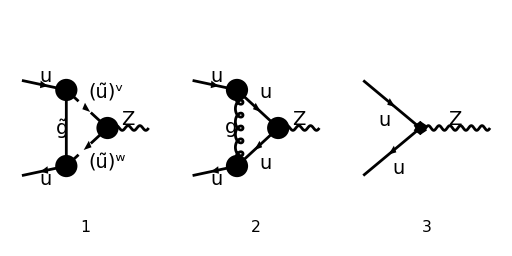

```mathematica
Paint[diag3[0], ColumnsXRows -> {3, 1}, Numbering -> Simple, ImageSize -> {512, 256}];
```

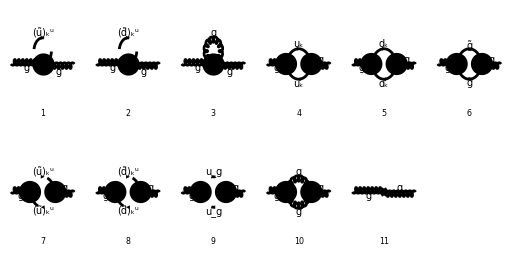

```mathematica
Paint[diag4[0], ColumnsXRows -> {6, 2}, Numbering -> Simple, ImageSize -> {512, 256}];
```

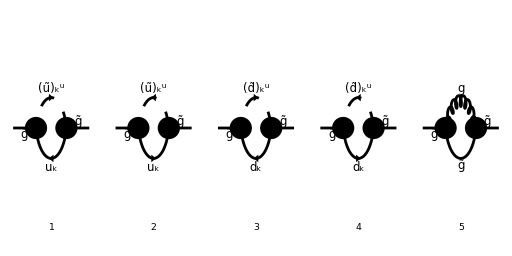

```mathematica
Paint[diag5[0], ColumnsXRows -> {5, 1}, Numbering -> Simple, ImageSize -> {512, 256}];
```

## Obtain the amplitudes

Some text.

```mathematica
MakeBoxes[mq, TraditionalForm] = SubscriptBox["m", "q"];

MakeBoxes[ZQL, TraditionalForm] = SubscriptBox["Z","qL"];
MakeBoxes[ZQR, TraditionalForm] = SubscriptBox["Z","qR"];
MakeBoxes[ZQ, TraditionalForm] = SubscriptBox["Z","q"];
MakeBoxes[Ze, TraditionalForm] = SubscriptBox["Z", "e"];
MakeBoxes[ZZ, TraditionalForm] = SubscriptBox["Z", "Z"];
MakeBoxes[ZsW, TraditionalForm] = SubscriptBox["Z", "sW"];
MakeBoxes[Zm, TraditionalForm] = SubscriptBox["Z", "m"];
MakeBoxes[ZGl, TraditionalForm] = SubscriptBox["Z", "g"];
MakeBoxes[ZGluino, TraditionalForm] = SubscriptBox["Z", OverscriptBox["g", "~"]];
MakeBoxes[ZmGluino, TraditionalForm] = SubscriptBox["Z", SubscriptBox["m", OverscriptBox["g", "~"]]];

MakeBoxes[dQL, TraditionalForm] = SubscriptBox["δ","qL"];
MakeBoxes[dQR, TraditionalForm] = SubscriptBox["δ","qR"];
MakeBoxes[dQ, TraditionalForm] = SubscriptBox["δ","q"];
MakeBoxes[de, TraditionalForm] = SubscriptBox["δ", "e"];
MakeBoxes[dZ, TraditionalForm] = SubscriptBox["δ", "Z"];
MakeBoxes[dsW, TraditionalForm] = SubscriptBox["δ", "W"];
MakeBoxes[dQm, TraditionalForm] = SubscriptBox["δ", "m"];
MakeBoxes[dGl, TraditionalForm] = SubscriptBox["δ", "g"];
MakeBoxes[dGluino, TraditionalForm] = SubscriptBox["δ", OverscriptBox["g", "~"]];
MakeBoxes[dmGluino, TraditionalForm] = SubscriptBox["δ", SubscriptBox["m", OverscriptBox["g", "~"]]];
```

### Quark self-energy

```mathematica
ampQuarkSE[0] = FCFAConvert[
	CreateFeynAmp[diagQuarkSE[1], Truncated -> True],
	IncomingMomenta -> {p},
	OutgoingMomenta -> {p},
	LorentzIndexNames -> {μ, ν},
	DropSumOver -> True,
	LoopMomenta -> {q},
	UndoChiralSplittings -> True,
	ChangeDimension -> D,
	List -> False,
	SMP -> True,
	FinalSubstitutions -> SMP["m_u"]->mq
] + FCFAConvert[
	CreateFeynAmp[diagQuarkSECT[1], Truncated -> True],
	IncomingMomenta -> {p},
	OutgoingMomenta -> {p},
	LorentzIndexNames -> {μ, ν},
	DropSumOver -> True,
	LoopMomenta -> {q},
	UndoChiralSplittings -> True,
	ChangeDimension -> D,
	List -> False,
	SMP -> True,
	FinalSubstitutions -> {dMf1[__]->Zm, dZfL1[__]->ZQL,
	dZfR1[__]->ZQR, SMP["m_u"]->mq}
] (*/. SqrtEGl -> 1*) // DiracSubstitute67
```

(ⅈ (ⅈ √2 (1/2-(γ̄)^5/2) Conjugate[SqrtEGl] g_s T_Col2Col3^Glu3 Conjugate[(R_Sfe32^((ũ)_1))]-ⅈ √2 SqrtEGl ((γ̄)^5/2+1/2) g_s T_Col2Col3^Glu3 Conjugate[(R_Sfe31^((ũ)_1))]).(m_(g̃)+γ·q).(ⅈ √2 SqrtEGl ((γ̄)^5/2+1/2) g_s T_Col3Col1^Glu3 R_Sfe32^((ũ)_1)-ⅈ √2 (1/2-(γ̄)^5/2) Conjugate[SqrtEGl] g_s T_Col3Col1^Glu3 R_Sfe31^((ũ)_1)))/(16 π^4 (q^2-m_(g̃)^2).((q-p)^2-m_((ũ)_(1,Sfe3))^2))-ⅈ (ⅈ (1/2-(γ̄)^5/2) δ_Col1Col2 (-1/2 m_q Conjugate[(Z_qR)]-(m_q Z_qL)/2-Z_m)+ⅈ ((γ̄)^5/2+1/2) δ_Col1Col2 (-1/2 m_q Conjugate[(Z_qL)]-(m_q Z_qR)/2-Z_m)+ⅈ δ_Col1Col2 (-Conjugate[(Z_qL)]/2-Z_qL/2) (-(γ·p)).(1/2-(γ̄)^5/2)+ⅈ δ_Col1Col2 (Conjugate[(Z_qR)]/2+Z_qR/2) (γ·p).((γ̄)^5/2+1/2))-(ⅈ g^μν (-ⅈ γ^ν g_s T_Col2Col3^Glu3).(m_q+γ·q).(-ⅈ γ^μ g_s T_Col3Col1^Glu3))/(16 π^4 (q^2-m_q^2).(q-p)^2)

### Gluon self - energy

```mathematica
ampGlSE[0] = Join[
	FCFAConvert[
		CreateFeynAmp[diagGlSE[1], Truncated -> True],
		IncomingMomenta -> {p},
		OutgoingMomenta -> {p},
		LorentzIndexNames -> {μ, ν},
		DropSumOver -> True,
		LoopMomenta -> {q},
		UndoChiralSplittings -> True,
		ChangeDimension -> D,
		List -> True,
		SMP -> True,
		FinalSubstitutions -> SMP["m_u"]->mq
	],
	FCFAConvert[
		CreateFeynAmp[diagGlSECT[1], Truncated -> True],
		IncomingMomenta -> {p},
		OutgoingMomenta -> {p},
		LorentzIndexNames -> {μ, ν},
		DropSumOver -> True,
		LoopMomenta -> {q},
		UndoChiralSplittings -> True,
		ChangeDimension -> D,
		List -> True,
		SMP -> True,
		FinalSubstitutions -> {dZGG1 -> ZGl, SMP["m_u"]->mq}
	]
]
```

{(ⅈ g^μν g_s^2 ((T^Glu1 T^Glu2)_Col3Col3+(T^Glu2 T^Glu1)_Col3Col3))/(16 π^4 (q^2-m_((ũ)_(Gen3,Sfe3))^2)),(ⅈ g^μν g_s^2 ((T^Glu1 T^Glu2)_Col3Col3+(T^Glu2 T^Glu1)_Col3Col3))/(16 π^4 (q^2-m_((d̃)_(Gen3,Sfe3))^2)),-(g^Lor3Lor4 (ⅈ g^Lor3ν g^Lor4μ f^Glu1Glu3$AL$15130 f^Glu2Glu3$AL$15130 g_s^2-ⅈ g^Lor3Lor4 g^μν (f^Glu1Glu3$AL$15131 f^Glu2Glu3$AL$15131+f^Glu1Glu3$AL$15132 f^Glu2Glu3$AL$15132) g_s^2+ⅈ g^Lor3μ g^Lor4ν f^Glu1Glu3$AL$15134 f^Glu2Glu3$AL$15134 g_s^2))/(32 π^4 q^2),-(ⅈ tr((MQU(Gen3)-γ·q).(-ⅈ γ^ν g_s T_Col3Col4^Glu2).(γ·(p-q)+MQU(Gen3)).(-ⅈ γ^μ g_s T_Col4Col3^Glu1)))/(16 π^4 (q^2-(MQU(Gen3))^2).((q-p)^2-(MQU(Gen3))^2)),-(ⅈ tr((MQD(Gen3)-γ·q).(-ⅈ γ^ν g_s T_Col3Col4^Glu2).(γ·(p-q)+MQD(Gen3)).(-ⅈ γ^μ g_s T_Col4Col3^Glu1)))/(16 π^4 (q^2-(MQD(Gen3))^2).((q-p)^2-(MQD(Gen3))^2)),-(ⅈ tr((m_(g̃)-γ·q).(-γ^ν g_s f^Glu2Glu3Glu4).(m_(g̃)+γ·(p-q)).(γ^μ g_s f^Glu1Glu3Glu4)))/(32 π^4 (q^2-m_(g̃)^2).((q-p)^2-m_(g̃)^2)),(ⅈ (p-2 q)^μ (2 q-p)^ν g_s^2 T_Col4Col3^Glu1 T_Col3Col4^Glu2)/(16 π^4 (q^2-m_((ũ)_(Gen3,Sfe3))^2).((q-p)^2-m_((ũ)_(Gen3,Sfe3))^2)),(ⅈ (p-2 q)^μ (2 q-p)^ν g_s^2 T_Col4Col3^Glu1 T_Col3Col4^Glu2)/(16 π^4 (q^2-m_((d̃)_(Gen3,Sfe3))^2).((q-p)^2-m_((d̃)_(Gen3,Sfe3))^2)),(ⅈ (q-p)^μ q^ν g_s^2 f^Glu1Glu3Glu4 f^Glu2Glu3Glu4)/(16 π^4 q^2.(q-p)^2),(ⅈ g^Lor3Lor4 g^Lor5Lor6 ((2 p-q)^Lor3 g^Lor5μ+g^Lor3μ (-p-q)^Lor5+g^Lor3Lor5 (2 q-p)^μ) ((q-2 p)^Lor4 g^Lor6ν+g^Lor4ν (p+q)^Lor6+g^Lor4Lor6 (p-2 q)^ν) g_s^2 f^Glu1Glu3Glu4 f^Glu2Glu3Glu4)/(32 π^4 q^2.(q-p)^2),-ⅈ (ⅈ Z_g p^μ p^ν δ^Glu1Glu2-ⅈ Z_g g^μν p^2 δ^Glu1Glu2)}

### Quark-Z vertex

```mathematica
ampQZVertex[0] = FCFAConvert[
	CreateFeynAmp[diagQuarkZVertex[1], Truncated -> True],
	IncomingMomenta -> {p, k},
	OutgoingMomenta -> {q},
	LorentzIndexNames -> {μ, ν},
	DropSumOver -> True,
	LoopMomenta -> {qloop},
	UndoChiralSplittings -> True,
	ChangeDimension -> D,
	List -> False,
	SMP -> True,
	FinalSubstitutions -> SMP["m_u"]->0
] + FCFAConvert[
	CreateFeynAmp[diagQuarkZVertex[0], Truncated -> True],
	IncomingMomenta -> {p, k},
	OutgoingMomenta -> {q},
	LorentzIndexNames -> {μ, ν},
	DropSumOver -> True,
	LoopMomenta -> {qloop},
	UndoChiralSplittings -> True,
	ChangeDimension -> D,
	List -> False,
	SMP -> True,
	FinalSubstitutions -> {SMP["m_u"]->0, DiracGamma[args__].DiracGamma[6] -> Ze*(ZQR+ZQR*)/2 DiracGamma[args].DiracGamma[6],
	DiracGamma[args__].DiracGamma[7] -> Ze*(ZQL+ZQL*)/2 DiracGamma[args].DiracGamma[7],
	SMP["sin_W"]->Sqrt[ZsW]*SMP["sin_W"], SMP["cos_W"]->SMP["cos_W"] - (1-Sqrt[ZsW])*SMP["sin_W"]^2/SMP["cos_W"]}
]
(*FCFAConvert[
	CreateFeynAmp[diagQuarkZVertexCT[1], Truncated -> True],
	IncomingMomenta -> {p, k},
	OutgoingMomenta -> {q},
	LorentzIndexNames -> {μ, ν},
	DropSumOver -> True,
	LoopMomenta -> {qloop},
	UndoChiralSplittings -> True,
	ChangeDimension -> D,
	List -> False,
	SMP -> True,
	FinalSubstitutions -> {dZfL1[__]->0,
	dZfR1[__]->0, dZe1->0, dSW1->0, dZZZ1->Ze*(ZQL+ZQR), dZAZ1->0}
]*)
```

-(ⅈ e (-2 k+q-2 qloop)^μ (4 (sin(θ_W))^2 R_Sfe52^((ũ)_1) Conjugate[(R_Sfe42^((ũ)_1))]+(4 (sin(θ_W))^2-3) R_Sfe51^((ũ)_1) Conjugate[(R_Sfe41^((ũ)_1))]) (ⅈ √2 (γ̄)^7 Conjugate[SqrtEGl] g_s T_Col2Col4^Glu4 Conjugate[(R_Sfe52^((ũ)_1))]-ⅈ √2 SqrtEGl (γ̄)^6 g_s T_Col2Col4^Glu4 Conjugate[(R_Sfe51^((ũ)_1))]).(m_(g̃)+γ·qloop).(ⅈ √2 SqrtEGl (γ̄)^6 g_s T_Col4Col1^Glu4 R_Sfe42^((ũ)_1)-ⅈ √2 (γ̄)^7 Conjugate[SqrtEGl] g_s T_Col4Col1^Glu4 R_Sfe41^((ũ)_1)))/(96 π^4 (cos(θ_W)) (sin(θ_W)) (qloop^2-m_(g̃)^2).((k+qloop)^2-m_((ũ)_(1,Sfe5))^2).((k-q+qloop)^2-m_((ũ)_(1,Sfe4))^2))+(g^Lor3ν (-ⅈ g_s γ^Lor3 T_Col2Col4^Glu4).(γ·(-k-qloop)).((2 ⅈ e γ^μ.(γ̄)^6 (sin(θ_W)))/(3 (cos(θ_W)))+(ⅈ e γ^μ.(γ̄)^7 (4 (sin(θ_W))^2-3))/(6 (cos(θ_W)) (sin(θ_W)))).(γ·(-k+q-qloop)).(-ⅈ γ^ν g_s T_Col4Col1^Glu4))/(16 π^4 qloop^2.(k+qloop)^2.(k-q+qloop)^2)-ⅈ ((ⅈ e Z_e γ^μ.(γ̄)^7 δ_Col1Col2 (Conjugate[(Z_qL)]+Z_qL) (4 Z_sW (sin(θ_W))^2-3))/(12 √Z_sW (sin(θ_W)) (cos(θ_W)-((1-√Z_sW) (sin(θ_W))^2)/(cos(θ_W))))+(ⅈ e Z_e √Z_sW γ^μ.(γ̄)^6 δ_Col1Col2 (Conjugate[(Z_qR)]+Z_qR) (sin(θ_W)))/(3 (cos(θ_W)-((1-√Z_sW) (sin(θ_W))^2)/(cos(θ_W)))))

```mathematica
FCFAConvert[
	CreateFeynAmp[diagQuarkZVertex[0], Truncated -> True],
	IncomingMomenta -> {p, k},
	OutgoingMomenta -> {q},
	LorentzIndexNames -> {μ, ν},
	DropSumOver -> True,
	LoopMomenta -> {qloop},
	UndoChiralSplittings -> True,
	ChangeDimension -> D,
	List -> False,
	SMP -> True,
	FinalSubstitutions -> {SMP["m_u"]->0, DiracGamma[args__].DiracGamma[6] -> Ze*(ZQR+ZQR*)/2 DiracGamma[args].DiracGamma[6],
	DiracGamma[args__].DiracGamma[7] -> Ze*(ZQL+ZQL*)/2 DiracGamma[args].DiracGamma[7]}
]
```

-ⅈ ((ⅈ e Z_e γ^μ.(γ̄)^7 δ_Col1Col2 (Conjugate[(Z_qL)]+Z_qL) (4 (sin(θ_W))^2-3))/(12 (cos(θ_W)) (sin(θ_W)))+(ⅈ e Z_e γ^μ.(γ̄)^6 δ_Col1Col2 (Conjugate[(Z_qR)]+Z_qR) (sin(θ_W)))/(3 (cos(θ_W))))

### Gluino self-energy

```mathematica
ampGluinoSE[0] = FCFAConvert[
	CreateFeynAmp[diagGluinoSE[1], Truncated -> True],
	IncomingMomenta -> {p},
	OutgoingMomenta -> {p},
	LorentzIndexNames -> {μ, ν},
	DropSumOver -> True,
	LoopMomenta -> {q},
	UndoChiralSplittings -> True,
	ChangeDimension -> D,
	List -> False,
	SMP -> True,
	FinalSubstitutions -> SMP["m_u"]->mq
] + FCFAConvert[
	CreateFeynAmp[diagQuarkSECT[1], Truncated -> True],
	IncomingMomenta -> {p},
	OutgoingMomenta -> {p},
	LorentzIndexNames -> {μ, ν},
	DropSumOver -> True,
	LoopMomenta -> {q},
	UndoChiralSplittings -> True,
	ChangeDimension -> D,
	List -> False,
	SMP -> True,
	FinalSubstitutions -> {dMf1[__]->ZmGluino, dZfL1[__]->ZGluino,
	dZfR1[__]->ZGluino, SMP["m_u"]->MGl,
	SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]] -> SUNTF[{SUNIndex[Glu2]},SUNFIndex[Col3],SUNFIndex[Col4]]SUNTF[{SUNIndex[Glu1]},SUNFIndex[Col4],SUNFIndex[Col3]]}
]
```

(ⅈ (ⅈ √2 Conjugate[SqrtEGl] Conjugate[(R_Sfe32^((d̃)_Gen3))] (γ̄)^7 g_s T_Col3Col4^Glu2-ⅈ √2 SqrtEGl Conjugate[(R_Sfe31^((d̃)_Gen3))] (γ̄)^6 g_s T_Col3Col4^Glu2).(γ·q+MQD(Gen3)).(ⅈ √2 SqrtEGl (γ̄)^6 g_s T_Col4Col3^Glu1 R_Sfe32^((d̃)_Gen3)-ⅈ √2 Conjugate[SqrtEGl] (γ̄)^7 g_s T_Col4Col3^Glu1 R_Sfe31^((d̃)_Gen3)))/(16 π^4 (q^2-(MQD(Gen3))^2).((q-p)^2-m_((d̃)_(Gen3,Sfe3))^2))+(ⅈ (ⅈ √2 SqrtEGl (γ̄)^6 g_s T_Col4Col3^Glu2 R_Sfe32^((d̃)_Gen3)-ⅈ √2 Conjugate[SqrtEGl] (γ̄)^7 g_s T_Col4Col3^Glu2 R_Sfe31^((d̃)_Gen3)).(γ·q+MQD(Gen3)).(ⅈ √2 Conjugate[SqrtEGl] Conjugate[(R_Sfe32^((d̃)_Gen3))] (γ̄)^7 g_s T_Col3Col4^Glu1-ⅈ √2 SqrtEGl Conjugate[(R_Sfe31^((d̃)_Gen3))] (γ̄)^6 g_s T_Col3Col4^Glu1))/(16 π^4 (q^2-(MQD(Gen3))^2).((q-p)^2-m_((d̃)_(Gen3,Sfe3))^2))+(ⅈ (ⅈ √2 Conjugate[SqrtEGl] Conjugate[(R_Sfe32^((ũ)_Gen3))] (γ̄)^7 g_s T_Col3Col4^Glu2-ⅈ √2 SqrtEGl Conjugate[(R_Sfe31^((ũ)_Gen3))] (γ̄)^6 g_s T_Col3Col4^Glu2).(γ·q+MQU(Gen3)).(ⅈ √2 SqrtEGl (γ̄)^6 g_s T_Col4Col3^Glu1 R_Sfe32^((ũ)_Gen3)-ⅈ √2 Conjugate[SqrtEGl] (γ̄)^7 g_s T_Col4Col3^Glu1 R_Sfe31^((ũ)_Gen3)))/(16 π^4 (q^2-(MQU(Gen3))^2).((q-p)^2-m_((ũ)_(Gen3,Sfe3))^2))+(ⅈ (ⅈ √2 SqrtEGl (γ̄)^6 g_s T_Col4Col3^Glu2 R_Sfe32^((ũ)_Gen3)-ⅈ √2 Conjugate[SqrtEGl] (γ̄)^7 g_s T_Col4Col3^Glu2 R_Sfe31^((ũ)_Gen3)).(γ·q+MQU(Gen3)).(ⅈ √2 Conjugate[SqrtEGl] Conjugate[(R_Sfe32^((ũ)_Gen3))] (γ̄)^7 g_s T_Col3Col4^Glu1-ⅈ √2 SqrtEGl Conjugate[(R_Sfe31^((ũ)_Gen3))] (γ̄)^6 g_s T_Col3Col4^Glu1))/(16 π^4 (q^2-(MQU(Gen3))^2).((q-p)^2-m_((ũ)_(Gen3,Sfe3))^2))-(ⅈ (-γ^ν g_s f^Glu2Glu3Glu4).(m_(g̃)+γ·q).(γ^μ g_s f^Glu1Glu3Glu4) g^μν)/(16 π^4 (q^2-m_(g̃)^2).(q-p)^2)-ⅈ (ⅈ (-1/2 m_(g̃) Z_(g̃)-Z_(m_(g̃))-1/2 m_(g̃) Conjugate[(Z_(g̃))]) (γ̄)^6 T_Col4Col3^Glu1 T_Col3Col4^Glu2+ⅈ (-1/2 m_(g̃) Z_(g̃)-Z_(m_(g̃))-1/2 m_(g̃) Conjugate[(Z_(g̃))]) (γ̄)^7 T_Col4Col3^Glu1 T_Col3Col4^Glu2+ⅈ (-(Z_(g̃))/2-Conjugate[(Z_(g̃))]/2) (-(γ·p)).(γ̄)^7 T_Col4Col3^Glu1 T_Col3Col4^Glu2+ⅈ ((Z_(g̃))/2+Conjugate[(Z_(g̃))]/2) (γ·p).(γ̄)^6 T_Col4Col3^Glu1 T_Col3Col4^Glu2)

## Calculate the amplitudes

### Quark self-energy

```mathematica
$Assumptions = {Subscript[θ, q]∈ Reals};
```

On-shell renormalisation of the quark field.

```mathematica
ClearScalarProducts[];
SPD[p, p] = 0;
```

```mathematica
ampQuarkSE[1] = ampQuarkSE[0] // DiracSimplify[#, DiracSubstitute5->True]& //
	ReplaceAll[#, {mq->0, Zm->0}]& //
	TID[#, q, UsePaVeBasis->True, ToPaVe->True]& //
	FCReplaceD[#, D->4-2Epsilon]&;
ampQuarkSE[2] = SelectFree2[ampQuarkSE[1], Index[Sfermion,3]] + (SelectNotFree2[ampQuarkSE[1], Index[Sfermion,3]] // Sum[#, {Index[Sfermion,3], 1, 2}]&) //
(*	ReplaceAll[#, {USf[3,1][1,1]->Cos[Subscript[θ, q]], USf[3,1][1,2]->Sin[Subscript[θ, q]], USf[3,1][2,1]->-Sin[Subscript[θ, q]], USf[3,1][2,2]->Cos[Subscript[θ, q]], SqrtEGl->1}]& //*)
	ReplaceAll[#, SqrtEGl*SqrtEGl -> 1]& //
	Refine //
	DiracSimplify
```

-(SqrtEGl^2 (γ̄)^6 g_s^2 R_12^((ũ)_1) m_(g̃) Conjugate[(R_11^((ũ)_1))] T_Col3Col1^Glu3 T_Col2Col3^Glu3 B_0(0,m_(g̃)^2,m_((ũ)_(1,1))^2))/(8 π^2)-(SqrtEGl^2 (γ̄)^6 g_s^2 R_22^((ũ)_1) m_(g̃) Conjugate[(R_21^((ũ)_1))] T_Col3Col1^Glu3 T_Col2Col3^Glu3 B_0(0,m_(g̃)^2,m_((ũ)_(1,2))^2))/(8 π^2)-((γ̄)^7 (Conjugate[SqrtEGl])^2 g_s^2 R_11^((ũ)_1) m_(g̃) Conjugate[(R_12^((ũ)_1))] T_Col3Col1^Glu3 T_Col2Col3^Glu3 B_0(0,m_(g̃)^2,m_((ũ)_(1,1))^2))/(8 π^2)-((γ̄)^7 (Conjugate[SqrtEGl])^2 g_s^2 R_21^((ũ)_1) m_(g̃) Conjugate[(R_22^((ũ)_1))] T_Col3Col1^Glu3 T_Col2Col3^Glu3 B_0(0,m_(g̃)^2,m_((ũ)_(1,2))^2))/(8 π^2)-(g_s^2 R_11^((ũ)_1) Conjugate[(R_11^((ũ)_1))] (γ·p).(γ̄)^7 T_Col3Col1^Glu3 T_Col2Col3^Glu3 B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2))/(8 π^2)-(g_s^2 R_12^((ũ)_1) Conjugate[(R_12^((ũ)_1))] (γ·p).(γ̄)^6 T_Col3Col1^Glu3 T_Col2Col3^Glu3 B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2))/(8 π^2)-(g_s^2 R_21^((ũ)_1) Conjugate[(R_21^((ũ)_1))] (γ·p).(γ̄)^7 T_Col3Col1^Glu3 T_Col2Col3^Glu3 B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2))/(8 π^2)-(g_s^2 R_22^((ũ)_1) Conjugate[(R_22^((ũ)_1))] (γ·p).(γ̄)^6 T_Col3Col1^Glu3 T_Col2Col3^Glu3 B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2))/(8 π^2)+1/2 δ_Col1Col2 Conjugate[(Z_qL)] (γ·p).(γ̄)^7+1/2 δ_Col1Col2 Conjugate[(Z_qR)] (γ·p).(γ̄)^6+1/2 Z_qL δ_Col1Col2 (γ·p).(γ̄)^7+1/2 Z_qR δ_Col1Col2 (γ·p).(γ̄)^6-(ε g_s^2 B_0(0,0,0) γ·p T_Col3Col1^Glu3 T_Col2Col3^Glu3)/(16 π^2)+(g_s^2 B_0(0,0,0) γ·p T_Col3Col1^Glu3 T_Col2Col3^Glu3)/(16 π^2)

Expanding in terms of gamma-5 matrix. Discarding the gamma-5 bit as it will not contribute in the end.

```mathematica
ampQuarkSE[3] = ampQuarkSE[2] // Collect2[#, {DiracGamma}, Factoring->Simplify]&
```

-(SqrtEGl^2 (γ̄)^6 g_s^2 m_(g̃) T_Col3Col1^Glu3 T_Col2Col3^Glu3 (R_12^((ũ)_1) Conjugate[(R_11^((ũ)_1))] B_0(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+R_22^((ũ)_1) Conjugate[(R_21^((ũ)_1))] B_0(0,m_(g̃)^2,m_((ũ)_(1,2))^2)))/(8 π^2)-((γ̄)^7 (Conjugate[SqrtEGl])^2 g_s^2 m_(g̃) T_Col3Col1^Glu3 T_Col2Col3^Glu3 (R_11^((ũ)_1) Conjugate[(R_12^((ũ)_1))] B_0(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+R_21^((ũ)_1) Conjugate[(R_22^((ũ)_1))] B_0(0,m_(g̃)^2,m_((ũ)_(1,2))^2)))/(8 π^2)+1/8 (γ·p).(γ̄)^7 (4 δ_Col1Col2 (Conjugate[(Z_qL)]+Z_qL)-(g_s^2 T_Col3Col1^Glu3 T_Col2Col3^Glu3 (R_11^((ũ)_1) Conjugate[(R_11^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+R_21^((ũ)_1) Conjugate[(R_21^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)))/π^2)+1/8 (γ·p).(γ̄)^6 (4 δ_Col1Col2 (Conjugate[(Z_qR)]+Z_qR)-(g_s^2 T_Col3Col1^Glu3 T_Col2Col3^Glu3 (R_12^((ũ)_1) Conjugate[(R_12^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+R_22^((ũ)_1) Conjugate[(R_22^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)))/π^2)-((ε-1) g_s^2 B_0(0,0,0) γ·p T_Col3Col1^Glu3 T_Col2Col3^Glu3)/(16 π^2)

Expanding ZQ =  1+dQ

```mathematica
ampQuarkSE[4] = ampQuarkSE[3] //
	ReplaceRepeated[#, {ZQL -> 1 + alpha dQL, ZQR -> 1 + alpha dQR, Zm -> 1 + alpha dQm}]& //
	Series[#, {alpha, 0, 1}]& //
	Normal // ReplaceAll[#, alpha->1]& //
	ReplaceAll[#, {dQL -> Re[dQL] + ⅈ*Im[dQL], dQR -> Re[dQR] + ⅈ*Im[dQR]}]& //
	SelectNotFree2[#, SMP["g_s"], dQL, dQR, dQm]&
```

-(SqrtEGl^2 (γ̄)^6 g_s^2 R_12^((ũ)_1) m_(g̃) Conjugate[(R_11^((ũ)_1))] T_Col3Col1^Glu3 T_Col2Col3^Glu3 B_0(0,m_(g̃)^2,m_((ũ)_(1,1))^2))/(8 π^2)-(SqrtEGl^2 (γ̄)^6 g_s^2 R_22^((ũ)_1) m_(g̃) Conjugate[(R_21^((ũ)_1))] T_Col3Col1^Glu3 T_Col2Col3^Glu3 B_0(0,m_(g̃)^2,m_((ũ)_(1,2))^2))/(8 π^2)-((γ̄)^7 (Conjugate[SqrtEGl])^2 g_s^2 R_11^((ũ)_1) m_(g̃) Conjugate[(R_12^((ũ)_1))] T_Col3Col1^Glu3 T_Col2Col3^Glu3 B_0(0,m_(g̃)^2,m_((ũ)_(1,1))^2))/(8 π^2)-((γ̄)^7 (Conjugate[SqrtEGl])^2 g_s^2 R_21^((ũ)_1) m_(g̃) Conjugate[(R_22^((ũ)_1))] T_Col3Col1^Glu3 T_Col2Col3^Glu3 B_0(0,m_(g̃)^2,m_((ũ)_(1,2))^2))/(8 π^2)-(g_s^2 (γ·p).(γ̄)^7 T_Col3Col1^Glu3 T_Col2Col3^Glu3 (R_11^((ũ)_1) Conjugate[(R_11^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+R_21^((ũ)_1) Conjugate[(R_21^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)))/(8 π^2)-(g_s^2 (γ·p).(γ̄)^6 T_Col3Col1^Glu3 T_Col2Col3^Glu3 (R_12^((ũ)_1) Conjugate[(R_12^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+R_22^((ũ)_1) Conjugate[(R_22^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)))/(8 π^2)+δ_Col1Col2 Re(δ_qL) (γ·p).(γ̄)^7+δ_Col1Col2 Re(δ_qR) (γ·p).(γ̄)^6-(ε g_s^2 B_0(0,0,0) γ·p T_Col3Col1^Glu3 T_Col2Col3^Glu3)/(16 π^2)+(g_s^2 B_0(0,0,0) γ·p T_Col3Col1^Glu3 T_Col2Col3^Glu3)/(16 π^2)

Now we can find the counterterm.

```mathematica
dSigma = D[ampQuarkSE[4], DiracGamma[Momentum[p,D],D]] /. DiracGamma[Momentum[p,D],D] -> 0 // DiracSimplify;
dSigmaL = Coefficient[dSigma, DiracGamma[7]] + SelectFree2[dSigma, DiracGamma[6|7]];
dSigmaR = Coefficient[dSigma, DiracGamma[6]] + SelectFree2[dSigma, DiracGamma[6|7]];
solL = Solve[dSigmaL==0, Re[dQL]] //
	Flatten // ReplaceAll[#,Rule[a_,b_]:>Rule[a,SUNSimplify[b]]]& //
	ReplaceAll[#, SMP["g_s"]^2 -> 4Pi SMP["alpha_s"]]&;
solR = Solve[dSigmaR==0, Re[dQR]] //
	Flatten // ReplaceAll[#,Rule[a_,b_]:>Rule[a,SUNSimplify[b]]]& //
	ReplaceAll[#, SMP["g_s"]^2 -> 4Pi SMP["alpha_s"]]&;
(*sol = Join[solL, solR]*)

sol[type_, gen_] := ReplaceAll[#, USf[3, 1] -> USf[type, gen]] &/@ Join[solL, solR]

sol[5, g]
```

{Re(δ_qL)→-(C_F α_s (-2 R_11^((q̃)_g) Conjugate[(R_11^((q̃)_g))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)-2 R_21^((q̃)_g) Conjugate[(R_21^((q̃)_g))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)-ε B_0(0,0,0)+B_0(0,0,0)))/(4 π),Re(δ_qR)→-(C_F α_s (-2 R_12^((q̃)_g) Conjugate[(R_12^((q̃)_g))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)-2 R_22^((q̃)_g) Conjugate[(R_22^((q̃)_g))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)-ε B_0(0,0,0)+B_0(0,0,0)))/(4 π)}

```mathematica
UnitaryUSf = {
	USf[__][1,1] -> Exp[ⅈ α]Cos[Subscript[θ, q]],
	USf[__][1,2] -> Exp[ⅈ β]Sin[Subscript[θ, q]],
	USf[__][2,1] -> -Exp[ⅈ(δ-β)]Sin[Subscript[θ, q]],
	USf[__][2,2] -> Exp[ⅈ (δ-α)]Cos[Subscript[θ, q]]
};
$Assumptions = Append[$Assumptions, {(α|β|δ|Subscript[θ, q]) ∈ Reals}]
```

{θ_q∈ℝ,{(α|β|δ|θ_q)∈ℝ}}

```mathematica
ampQuarkSE[4] /. DiracGamma[Momentum[p,D],D] -> mq /. SMP["g_s"]^2 -> 4Pi SMP["alpha_s"] /. SqrtEGl -> Exp[ⅈ Subscript[ϕ, g]] /. sol[3,1] /. DiracGamma[6] -> 1-DiracGamma[7] /. UnitaryUSf //
	Simplify[#, Assumptions -> {(α|β|δ|Subscript[θ, q]|Subscript[ϕ, g]) ∈ Reals}]& // SUNSimplify
```

-(C_F α_s m_(g̃) δ_Col1Col2 sin(2 θ_q) ⅇ^(-ⅈ α-ⅈ β-2 ⅈ ϕ_g) (ⅇ^(2 ⅈ α) (γ̄)^7-(γ̄)^7 ⅇ^(2 ⅈ β+4 ⅈ ϕ_g)+ⅇ^(2 ⅈ β+4 ⅈ ϕ_g)) (B_0(0,m_(g̃)^2,m_((ũ)_(1,1))^2)-B_0(0,m_(g̃)^2,m_((ũ)_(1,2))^2)))/(4 π)

```mathematica
Export[FileNameJoin[{ResultsDir, "quarkCTs.m"}], sol[type, gen] // FullForm // ToString];
```

### Gluon self-energy

Some text

```mathematica
ampGlSE[1] = 2Nf ampGlSE[0][[1]] + ampGlSE[0][[3]] + Nf  ampGlSE[0][[4]] + ampGlSE[0][[6]] + 2Nf ampGlSE[0][[7]]  + Total[ampGlSE[0][[9;;]]] //
   	ReplaceAll[#, MQU[arg_] -> SMP["m_q"]] &;
ampGlSE[2] = ampGlSE[1] // DiracSimplify //
     	SUNSimplify // DiracSimplify //
   	TID[#, q, UsePaVeBasis -> True, ToPaVe -> True] &;
```

Discard all the finite pieces of the 1-loop amplitude.

```mathematica
ampGlSEDiv[0] = ampGlSE[2] // PaVeUVPart[#]& // ReplaceRepeated[#, SqrtEGl SqrtEGl*->1]&;
```

```mathematica
ampGlSEDiv[1] = FCReplaceD[ampGlSEDiv[0], D->4-2Epsilon] //
	Series[#,{Epsilon,0,0}]& //
	Normal // FCHideEpsilon // Simplify
```

(δ^Glu1Glu2 (3 p^μ p^ν (16 π^2 Z_g-(Δ+ℽ-log(4 π)) g_s^2 (C_A-N_f))-4 g_s^2 g^μν (C_A m_(g̃)^2-N_f m_((ũ)_(Gen3,Sfe3))^2+N_f m_q^2)))/(48 π^2)

```mathematica
ampGlSEDiv[2] = ampGlSEDiv[1] //
	ReplaceRepeated[#,{
		ZGl -> 1 + alpha dGl}
	]& //
	Series[#,{alpha,0,1}]& //
	Normal // ReplaceAll[#, alpha->1]& //
	SelectNotFree2[#, SMP["Delta"], dGl]&
```

δ_g p^μ p^ν δ^Glu1Glu2-(Δ g_s^2 p^μ p^ν δ^Glu1Glu2 (C_A-N_f))/(16 π^2)

```mathematica
ampGlSEDiv[3] = ampGlSEDiv[2] //
	SUNSimplify //
	Collect2[#, Pair[__], Factoring->Simplify]&
```

(p^μ p^ν δ^Glu1Glu2 (Δ g_s^2 (N_f-C_A)+16 π^2 δ_g))/(16 π^2)

```mathematica
solGlMS = Solve[ampGlSEDiv[3]==0, dGl] //
	Flatten // ReplaceAll[#,Rule[a_,b_]:>Rule[a,SUNSimplify[b]]]& //
	ReplaceAll[#, SMP["g_s"]^2 -> 4Pi SMP["alpha_s"]]&
```

{δ_g→-(Δ α_s (N_f-C_A))/(4 π)}

### Quark-Z Vertex

```mathematica
ampQZVertex[1] = ampQZVertex[0] // SUNSimplify // DiracSimplify // ReplaceRepeated[#, {SqrtEGl->0}]&;
```

```mathematica
ampQZVertex[2] = TID[ampQZVertex[1], qloop, UsePaVeBasis -> True, ToPaVe -> True];
```

```mathematica
ampQZVertexDiv[0] = ampQZVertex[2] // PaVeUVPart // ReplaceAll[#, SqrtEGl*SqrtEGl*->1]&
```

(e (C_A-2 C_F) δ_Col1Col2 (32 π^2 D C_A Z_e Z_sW γ^μ.(γ̄)^7 Conjugate[(Z_qL)] (cos(θ_W))^2 (sin(θ_W))^2-24 π^2 D C_A Z_e γ^μ.(γ̄)^7 Conjugate[(Z_qL)] (cos(θ_W))^2+32 π^2 D C_A Z_e Z_sW γ^μ.(γ̄)^6 Conjugate[(Z_qR)] (cos(θ_W))^2 (sin(θ_W))^2-128 π^2 C_A Z_e Z_sW γ^μ.(γ̄)^7 Conjugate[(Z_qL)] (cos(θ_W))^2 (sin(θ_W))^2+96 π^2 C_A Z_e γ^μ.(γ̄)^7 Conjugate[(Z_qL)] (cos(θ_W))^2-128 π^2 C_A Z_e Z_sW γ^μ.(γ̄)^6 Conjugate[(Z_qR)] (cos(θ_W))^2 (sin(θ_W))^2+32 π^2 D C_A Z_e Z_qL Z_sW γ^μ.(γ̄)^7 (cos(θ_W))^2 (sin(θ_W))^2-24 π^2 D C_A Z_e Z_qL γ^μ.(γ̄)^7 (cos(θ_W))^2+32 π^2 D C_A Z_e Z_qR Z_sW γ^μ.(γ̄)^6 (cos(θ_W))^2 (sin(θ_W))^2-128 π^2 C_A Z_e Z_qL Z_sW γ^μ.(γ̄)^7 (cos(θ_W))^2 (sin(θ_W))^2+96 π^2 C_A Z_e Z_qL γ^μ.(γ̄)^7 (cos(θ_W))^2-128 π^2 C_A Z_e Z_qR Z_sW γ^μ.(γ̄)^6 (cos(θ_W))^2 (sin(θ_W))^2-4 C_A^2 g_s^2 √Z_sW γ^μ.(γ̄)^6 (cos(θ_W))^2 (sin(θ_W))^2-4 C_A^2 g_s^2 √Z_sW γ^μ.(γ̄)^7 (cos(θ_W))^2 (sin(θ_W))^2+3 C_A^2 g_s^2 √Z_sW γ^μ.(γ̄)^7 (cos(θ_W))^2-4 C_A^2 g_s^2 Z_sW γ^μ.(γ̄)^6 (sin(θ_W))^4+4 C_A^2 g_s^2 √Z_sW γ^μ.(γ̄)^6 (sin(θ_W))^4-4 C_A^2 g_s^2 Z_sW γ^μ.(γ̄)^7 (sin(θ_W))^4+4 C_A^2 g_s^2 √Z_sW γ^μ.(γ̄)^7 (sin(θ_W))^4+3 C_A^2 g_s^2 Z_sW γ^μ.(γ̄)^7 (sin(θ_W))^2-3 C_A^2 g_s^2 √Z_sW γ^μ.(γ̄)^7 (sin(θ_W))^2+4 g_s^2 √Z_sW γ^μ.(γ̄)^6 (cos(θ_W))^2 (sin(θ_W))^2+4 g_s^2 √Z_sW γ^μ.(γ̄)^7 (cos(θ_W))^2 (sin(θ_W))^2-3 g_s^2 √Z_sW γ^μ.(γ̄)^7 (cos(θ_W))^2+4 g_s^2 Z_sW γ^μ.(γ̄)^6 (sin(θ_W))^4-4 g_s^2 √Z_sW γ^μ.(γ̄)^6 (sin(θ_W))^4+4 g_s^2 Z_sW γ^μ.(γ̄)^7 (sin(θ_W))^4-4 g_s^2 √Z_sW γ^μ.(γ̄)^7 (sin(θ_W))^4-3 g_s^2 Z_sW γ^μ.(γ̄)^7 (sin(θ_W))^2+3 g_s^2 √Z_sW γ^μ.(γ̄)^7 (sin(θ_W))^2))/(96 π^2 (D-4) √Z_sW (cos(θ_W)) (sin(θ_W)) ((cos(θ_W))^2+√Z_sW (sin(θ_W))^2-(sin(θ_W))^2))

```mathematica
ampQZVertexDiv[1] = FCReplaceD[ampQZVertexDiv[0], D -> 4 - 2 Epsilon] // 
      	Series[#, {Epsilon, 0, 0}] & //
     	Normal // FCHideEpsilon // SUNSimplify;
```

```mathematica
ampQZVertexDiv[2] = ampQZVertexDiv[1] // ReplaceRepeated[#, {
          	Ze -> 1 + alpha de, 
          	ZZ -> 1 + alpha dZ, 
          	ZQL -> 1 + alpha dQL,
          	ZQR -> 1 + alpha dQR,
          	ZsW -> 1 + alpha dsW
          	}] & // ReplaceAll[#, (alpha*b_)*->alpha*b*]& // Expand // Series[#, {alpha, 0, 1}] & // 
     	Normal // ReplaceAll[#, alpha -> 1] & //
   	SelectNotFree2[#, SMP["Delta"], de, dZ, dQL, dQR, dsW] &
```

(C_A^3 δ_W γ^μ.(γ̄)^6 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(96 π^2 (cos(θ_W))^5)-(C_A δ_W γ^μ.(γ̄)^6 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(96 π^2 (cos(θ_W))^5)-(C_A^2 C_F δ_W γ^μ.(γ̄)^6 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(48 π^2 (cos(θ_W))^5)+(C_F δ_W γ^μ.(γ̄)^6 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(48 π^2 (cos(θ_W))^5)+(C_A^3 δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(96 π^2 (cos(θ_W))^5)-(C_A δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(96 π^2 (cos(θ_W))^5)-(C_A^2 C_F δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(48 π^2 (cos(θ_W))^5)+(C_F δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(48 π^2 (cos(θ_W))^5)+(C_A^3 δ_W ℽ γ^μ.(γ̄)^6 e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(96 π^2 (cos(θ_W))^5)-(C_A δ_W ℽ γ^μ.(γ̄)^6 e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(96 π^2 (cos(θ_W))^5)-(C_A^2 C_F δ_W ℽ γ^μ.(γ̄)^6 e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(48 π^2 (cos(θ_W))^5)+(C_F δ_W ℽ γ^μ.(γ̄)^6 e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(48 π^2 (cos(θ_W))^5)+(C_A^3 δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(96 π^2 (cos(θ_W))^5)-(C_A δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(96 π^2 (cos(θ_W))^5)-(C_A^2 C_F δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(48 π^2 (cos(θ_W))^5)+(C_F δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(48 π^2 (cos(θ_W))^5)-(C_A^3 δ_W γ^μ.(γ̄)^6 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(96 π^2 (cos(θ_W))^5)+(C_A δ_W γ^μ.(γ̄)^6 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(96 π^2 (cos(θ_W))^5)+(C_A^2 C_F δ_W γ^μ.(γ̄)^6 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(48 π^2 (cos(θ_W))^5)-(C_F δ_W γ^μ.(γ̄)^6 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(48 π^2 (cos(θ_W))^5)-(C_A^3 δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(96 π^2 (cos(θ_W))^5)+(C_A δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(96 π^2 (cos(θ_W))^5)+(C_A^2 C_F δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(48 π^2 (cos(θ_W))^5)-(C_F δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^5)/(48 π^2 (cos(θ_W))^5)+(C_A^3 δ_W γ^μ.(γ̄)^6 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^3)-(C_A δ_W γ^μ.(γ̄)^6 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^3)-(C_A^2 C_F δ_W γ^μ.(γ̄)^6 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^3)+(C_F δ_W γ^μ.(γ̄)^6 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^3)+(C_A^3 δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^3)-(C_A δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^3)-(C_A^2 C_F δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^3)+(C_F δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^3)-(C_A^3 δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(128 π^2 (cos(θ_W))^5)+(C_A δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(128 π^2 (cos(θ_W))^5)+(C_A^2 C_F δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(64 π^2 (cos(θ_W))^5)-(C_F δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(64 π^2 (cos(θ_W))^5)+(C_A^3 δ_W ℽ γ^μ.(γ̄)^6 e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^3)-(C_A δ_W ℽ γ^μ.(γ̄)^6 e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^3)-(C_A^2 C_F δ_W ℽ γ^μ.(γ̄)^6 e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^3)+(C_F δ_W ℽ γ^μ.(γ̄)^6 e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^3)+(C_A^3 δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^3)-(C_A δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^3)-(C_A^2 C_F δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^3)+(C_F δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^3)-(C_A^3 δ_W γ^μ.(γ̄)^6 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^3)+(C_A δ_W γ^μ.(γ̄)^6 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^3)+(C_A^2 C_F δ_W γ^μ.(γ̄)^6 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^3)-(C_F δ_W γ^μ.(γ̄)^6 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^3)-(C_A^3 δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^3)+(C_A δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^3)+(C_A^2 C_F δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^3)-(C_F δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^3)-(C_A^3 δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(128 π^2 (cos(θ_W))^5)+(C_A δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(128 π^2 (cos(θ_W))^5)+(C_A^2 C_F δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(64 π^2 (cos(θ_W))^5)-(C_F δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(64 π^2 (cos(θ_W))^5)+(C_A^3 δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(128 π^2 (cos(θ_W))^5)-(C_A δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(128 π^2 (cos(θ_W))^5)-(C_A^2 C_F δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(64 π^2 (cos(θ_W))^5)+(C_F δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W))^3)/(64 π^2 (cos(θ_W))^5)-(C_A^3 δ_W γ^μ.(γ̄)^6 Δ e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^5)+(C_A δ_W γ^μ.(γ̄)^6 Δ e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^5)+(C_A^2 C_F δ_W γ^μ.(γ̄)^6 Δ e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^5)-(C_F δ_W γ^μ.(γ̄)^6 Δ e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^5)-(C_A^3 δ_W γ^μ.(γ̄)^7 Δ e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^5)+(C_A δ_W γ^μ.(γ̄)^7 Δ e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^5)+(C_A^2 C_F δ_W γ^μ.(γ̄)^7 Δ e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^5)-(C_F δ_W γ^μ.(γ̄)^7 Δ e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^5)-(C_A^3 δ_W ℽ γ^μ.(γ̄)^6 e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^5)+(C_A δ_W ℽ γ^μ.(γ̄)^6 e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^5)+(C_A^2 C_F δ_W ℽ γ^μ.(γ̄)^6 e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^5)-(C_F δ_W ℽ γ^μ.(γ̄)^6 e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^5)-(C_A^3 δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^5)+(C_A δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^5)+(C_A^2 C_F δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^5)-(C_F δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^5)+(C_A^3 δ_W γ^μ.(γ̄)^6 log(4 π) e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^5)-(C_A δ_W γ^μ.(γ̄)^6 log(4 π) e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^5)-(C_A^2 C_F δ_W γ^μ.(γ̄)^6 log(4 π) e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^5)+(C_F δ_W γ^μ.(γ̄)^6 log(4 π) e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^5)+(C_A^3 δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^5)-(C_A δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(96 π^2 (cos(θ_W))^5)-(C_A^2 C_F δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^5)+(C_F δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W))^3)/(48 π^2 (cos(θ_W))^5)+(C_A^3 γ^μ.(γ̄)^6 Δ e g_s^2 δ_Col1Col2 (sin(θ_W)))/(48 π^2 (cos(θ_W)))-(C_A γ^μ.(γ̄)^6 Δ e g_s^2 δ_Col1Col2 (sin(θ_W)))/(48 π^2 (cos(θ_W)))-(C_A^2 C_F γ^μ.(γ̄)^6 Δ e g_s^2 δ_Col1Col2 (sin(θ_W)))/(24 π^2 (cos(θ_W)))+(C_F γ^μ.(γ̄)^6 Δ e g_s^2 δ_Col1Col2 (sin(θ_W)))/(24 π^2 (cos(θ_W)))+(C_A^3 γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W)))/(48 π^2 (cos(θ_W)))-(C_A γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W)))/(48 π^2 (cos(θ_W)))-(C_A^2 C_F γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W)))/(24 π^2 (cos(θ_W)))+(C_F γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W)))/(24 π^2 (cos(θ_W)))-(C_A^3 δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W)))/(128 π^2 (cos(θ_W))^3)+(C_A δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W)))/(128 π^2 (cos(θ_W))^3)+(C_A^2 C_F δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W)))/(64 π^2 (cos(θ_W))^3)-(C_F δ_W γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2 (sin(θ_W)))/(64 π^2 (cos(θ_W))^3)-(C_A^3 δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W)))/(128 π^2 (cos(θ_W))^3)+(C_A δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W)))/(128 π^2 (cos(θ_W))^3)+(C_A^2 C_F δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W)))/(64 π^2 (cos(θ_W))^3)-(C_F δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 δ_Col1Col2 (sin(θ_W)))/(64 π^2 (cos(θ_W))^3)+(C_A^3 δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W)))/(128 π^2 (cos(θ_W))^3)-(C_A δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W)))/(128 π^2 (cos(θ_W))^3)-(C_A^2 C_F δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W)))/(64 π^2 (cos(θ_W))^3)+(C_F δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 δ_Col1Col2 (sin(θ_W)))/(64 π^2 (cos(θ_W))^3)+(2 C_A^2 δ_e γ^μ.(γ̄)^6 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))-(4 C_A C_F δ_e γ^μ.(γ̄)^6 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))+(C_A^2 δ_qR γ^μ.(γ̄)^6 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))-(2 C_A C_F δ_qR γ^μ.(γ̄)^6 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))+(2 C_A^2 δ_W γ^μ.(γ̄)^6 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))-(4 C_A C_F δ_W γ^μ.(γ̄)^6 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))+(C_A^2 Conjugate[(δ_qR)] γ^μ.(γ̄)^6 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))-(2 C_A C_F Conjugate[(δ_qR)] γ^μ.(γ̄)^6 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))+(2 C_A^2 δ_e γ^μ.(γ̄)^7 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))-(4 C_A C_F δ_e γ^μ.(γ̄)^7 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))+(C_A^2 δ_qL γ^μ.(γ̄)^7 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))-(2 C_A C_F δ_qL γ^μ.(γ̄)^7 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))+(2 C_A^2 δ_W γ^μ.(γ̄)^7 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))-(4 C_A C_F δ_W γ^μ.(γ̄)^7 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))+(C_A^2 Conjugate[(δ_qL)] γ^μ.(γ̄)^7 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))-(2 C_A C_F Conjugate[(δ_qL)] γ^μ.(γ̄)^7 e δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))+(C_A^3 δ_W γ^μ.(γ̄)^7 Δ e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(128 π^2 (cos(θ_W))^5)-(C_A δ_W γ^μ.(γ̄)^7 Δ e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(128 π^2 (cos(θ_W))^5)-(C_A^2 C_F δ_W γ^μ.(γ̄)^7 Δ e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(64 π^2 (cos(θ_W))^5)+(C_F δ_W γ^μ.(γ̄)^7 Δ e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(64 π^2 (cos(θ_W))^5)+(C_A^3 δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(128 π^2 (cos(θ_W))^5)-(C_A δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(128 π^2 (cos(θ_W))^5)-(C_A^2 C_F δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(64 π^2 (cos(θ_W))^5)+(C_F δ_W ℽ γ^μ.(γ̄)^7 e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(64 π^2 (cos(θ_W))^5)-(C_A^3 δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(128 π^2 (cos(θ_W))^5)+(C_A δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(128 π^2 (cos(θ_W))^5)+(C_A^2 C_F δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(64 π^2 (cos(θ_W))^5)-(C_F δ_W γ^μ.(γ̄)^7 log(4 π) e g_s^2 ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(64 π^2 (cos(θ_W))^5)-(C_A^2 δ_W γ^μ.(γ̄)^6 e ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W))^3)+(2 C_A C_F δ_W γ^μ.(γ̄)^6 e ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W))^3)-(C_A^2 δ_W γ^μ.(γ̄)^7 e ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W))^3)+(2 C_A C_F δ_W γ^μ.(γ̄)^7 e ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W))^3)-(C_A^3 γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2)/(64 π^2 (cos(θ_W)) (sin(θ_W)))+(C_A γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2)/(64 π^2 (cos(θ_W)) (sin(θ_W)))+(C_A^2 C_F γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2)/(32 π^2 (cos(θ_W)) (sin(θ_W)))-(C_F γ^μ.(γ̄)^7 Δ e g_s^2 δ_Col1Col2)/(32 π^2 (cos(θ_W)) (sin(θ_W)))-(C_A^2 δ_e γ^μ.(γ̄)^7 e δ_Col1Col2)/(2 (cos(θ_W)) (sin(θ_W)))+(C_A C_F δ_e γ^μ.(γ̄)^7 e δ_Col1Col2)/((cos(θ_W)) (sin(θ_W)))-(C_A^2 δ_qL γ^μ.(γ̄)^7 e δ_Col1Col2)/(4 (cos(θ_W)) (sin(θ_W)))+(C_A C_F δ_qL γ^μ.(γ̄)^7 e δ_Col1Col2)/(2 (cos(θ_W)) (sin(θ_W)))-(C_A^2 Conjugate[(δ_qL)] γ^μ.(γ̄)^7 e δ_Col1Col2)/(4 (cos(θ_W)) (sin(θ_W)))+(C_A C_F Conjugate[(δ_qL)] γ^μ.(γ̄)^7 e δ_Col1Col2)/(2 (cos(θ_W)) (sin(θ_W)))+(C_A^2 δ_W γ^μ.(γ̄)^7 e ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2)/(4 (cos(θ_W))^3 (sin(θ_W)))-(C_A C_F δ_W γ^μ.(γ̄)^7 e ((cos(θ_W))^2+(sin(θ_W))^2) δ_Col1Col2)/(2 (cos(θ_W))^3 (sin(θ_W)))

```mathematica
ampQZVertexDiv[3] = ampQZVertexDiv[2] // SUNSimplify[#, Explicit -> True] & // 
   	ReplaceAll[#, SUNTrace[x__] :> SUNTrace[x, Explicit -> True]] & //
  	Collect2[#, Epsilon, SUNIndex] &
```

1/(192 π^2 (cos(θ_W))^3 (sin(θ_W)))e (C_A-2 C_F) δ_Col1Col2 (64 π^2 C_A γ^μ.(γ̄)^7 Conjugate[(δ_qL)] (cos(θ_W))^2 (sin(θ_W))^2-48 π^2 C_A γ^μ.(γ̄)^7 Conjugate[(δ_qL)] (cos(θ_W))^2+64 π^2 C_A γ^μ.(γ̄)^6 Conjugate[(δ_qR)] (cos(θ_W))^2 (sin(θ_W))^2+128 π^2 C_A δ_e γ^μ.(γ̄)^6 (cos(θ_W))^2 (sin(θ_W))^2+128 π^2 C_A δ_e γ^μ.(γ̄)^7 (cos(θ_W))^2 (sin(θ_W))^2-96 π^2 C_A δ_e γ^μ.(γ̄)^7 (cos(θ_W))^2+4 Δ C_A^2 g_s^2 γ^μ.(γ̄)^6 (cos(θ_W))^2 (sin(θ_W))^2+4 Δ C_A^2 g_s^2 γ^μ.(γ̄)^7 (cos(θ_W))^2 (sin(θ_W))^2-3 Δ C_A^2 g_s^2 γ^μ.(γ̄)^7 (cos(θ_W))^2+64 π^2 C_A δ_qL γ^μ.(γ̄)^7 (cos(θ_W))^2 (sin(θ_W))^2-48 π^2 C_A δ_qL γ^μ.(γ̄)^7 (cos(θ_W))^2+64 π^2 C_A δ_qR γ^μ.(γ̄)^6 (cos(θ_W))^2 (sin(θ_W))^2+64 π^2 C_A δ_W γ^μ.(γ̄)^6 (cos(θ_W))^2 (sin(θ_W))^2+64 π^2 C_A δ_W γ^μ.(γ̄)^7 (cos(θ_W))^2 (sin(θ_W))^2+48 π^2 C_A δ_W γ^μ.(γ̄)^7 (cos(θ_W))^2-64 π^2 C_A δ_W γ^μ.(γ̄)^6 (sin(θ_W))^4-64 π^2 C_A δ_W γ^μ.(γ̄)^7 (sin(θ_W))^4+48 π^2 C_A δ_W γ^μ.(γ̄)^7 (sin(θ_W))^2-4 Δ g_s^2 γ^μ.(γ̄)^6 (cos(θ_W))^2 (sin(θ_W))^2-4 Δ g_s^2 γ^μ.(γ̄)^7 (cos(θ_W))^2 (sin(θ_W))^2+3 Δ g_s^2 γ^μ.(γ̄)^7 (cos(θ_W))^2)

```mathematica
ampQZVertexDiv[4] = ampQZVertexDiv[3] // 
      	ReplaceAll[#, suntf[xx_, _SUNFIndex, _SUNFIndex] :> SUNT @@ xx] & // 
     	ReplaceAll[#, SUNTF -> suntf] & // ReplaceAll[#, 
      	suntf[xx_, _SUNFIndex, _SUNFIndex] :> SUNT @@ xx] & // 
   	SUNSimplify // Collect2[#, {dQL, dQR, de, dsW, SMP["g_s"]^2}, Factoring->Simplify] & // ReplaceRepeated[#, DiracGamma[args__].DiracGamma[6]+DiracGamma[args__].DiracGamma[7]->DiracGamma[args]]&
```

(e C_A γ^μ.(γ̄)^7 (C_A-2 C_F) δ_Col1Col2 Conjugate[(δ_qL)] (4 (sin(θ_W))^2-3))/(12 (cos(θ_W)) (sin(θ_W)))+(e C_A γ^μ.(γ̄)^6 (C_A-2 C_F) δ_Col1Col2 Conjugate[(δ_qR)] (sin(θ_W)))/(3 (cos(θ_W)))+(e C_A δ_e (C_A-2 C_F) δ_Col1Col2 (4 γ^μ.(γ̄)^6 (sin(θ_W))^2+γ^μ.(γ̄)^7 (4 (sin(θ_W))^2-3)))/(6 (cos(θ_W)) (sin(θ_W)))+(Δ e (C_A^2-1) g_s^2 (C_A-2 C_F) δ_Col1Col2 (4 γ^μ.(γ̄)^6 (sin(θ_W))^2+γ^μ.(γ̄)^7 (4 (sin(θ_W))^2-3)))/(192 π^2 (cos(θ_W)) (sin(θ_W)))+(e C_A δ_qL γ^μ.(γ̄)^7 (C_A-2 C_F) δ_Col1Col2 (4 (sin(θ_W))^2-3))/(12 (cos(θ_W)) (sin(θ_W)))+(e C_A δ_qR γ^μ.(γ̄)^6 (C_A-2 C_F) δ_Col1Col2 (sin(θ_W)))/(3 (cos(θ_W)))+(e C_A δ_W (C_A-2 C_F) δ_Col1Col2 (4 γ^μ.(γ̄)^6 (sin(θ_W))^2 ((cos(θ_W))^2-(sin(θ_W))^2)+γ^μ.(γ̄)^7 ((cos(θ_W))^2 (4 (sin(θ_W))^2+3)-4 (sin(θ_W))^4+3 (sin(θ_W))^2)))/(12 (cos(θ_W))^3 (sin(θ_W)))

```mathematica
CommonFactor = (SMP["e"](CA-2CF))/(48π^2*SMP["cos_W"])SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]];
CommonFactor Collect2[ampQZVertexDiv[4]/CommonFactor, DiracGamma[__].DiracGamma[6|7], Factoring -> (Collect2[#, {dQL, dQR, de, SMP["g_s"]^2}, Factoring->Simplify]&)]
```

1/(48 π^2 (cos(θ_W)))e (C_A-2 C_F) δ_Col1Col2 (γ^μ.(γ̄)^7 ((4 π^2 C_A Conjugate[(δ_qL)] (4 (sin(θ_W))^2-3))/(sin(θ_W))+(4 π^2 C_A δ_W ((cos(θ_W))^2 (4 (sin(θ_W))^2+3)-4 (sin(θ_W))^4+3 (sin(θ_W))^2))/((cos(θ_W))^2 (sin(θ_W)))+(8 π^2 C_A δ_e (4 (sin(θ_W))^2-3))/(sin(θ_W))+(Δ (C_A^2-1) g_s^2 (4 (sin(θ_W))^2-3))/(4 (sin(θ_W)))+(4 π^2 C_A δ_qL (4 (sin(θ_W))^2-3))/(sin(θ_W)))+γ^μ.(γ̄)^6 (16 π^2 C_A Conjugate[(δ_qR)] (sin(θ_W))+(16 π^2 C_A δ_W (sin(θ_W)) ((cos(θ_W))^2-(sin(θ_W))^2))/(cos(θ_W))^2+32 π^2 C_A δ_e (sin(θ_W))+Δ (C_A^2-1) g_s^2 (sin(θ_W))+16 π^2 C_A δ_qR (sin(θ_W))))

```mathematica
ampQZVertexDiv[5] = (ampQZVertexDiv[4] /. {
(*         	SMP["d_A"] -> SMP["d_A^MS"], 
         	SMP["d_psi"] -> Re[SMP["d_psi^MS"]] + ⅈ*Im[SMP["d_psi"]]*0,*)
         	dQR -> Re[dQR] + ⅈ*Im[dQR],
         	dQL -> Re[dQL] + ⅈ*Im[dQL](*,
         	SMP["Delta"] -> 1/Epsilon*)
         } /. solQMS ) // ReplaceAll[#, SMP["g_s"]^2 -> 4 Pi SMP["alpha_s"]] & //
    Collect2[#, Epsilon] & // SUNSimplify
```

ReplaceAll::reps: {solQMS} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FCCanonicalizeDummyIndices::failmsg: Error! FCCanonicalizeDummyIndices has encountered a fatal problem and must abort the computation. The problem reads: The input expression contains dummy indices that
			appear more than twice, which violates the Einstein convention.

$Aborted

```mathematica
Collect2[ampQZVertexDiv[5], DiracGamma[__].DiracGamma[6|7], Factoring->Simplify]
```

ampQZVertexDiv(5)

```mathematica
ampQZVertexDivL = SelectNotFree2[ampQZVertexDiv[5], DiracGamma[__].DiracGamma[7]] /. DiracGamma[__].DiracGamma[7]->1;
ampQZVertexDivR = SelectNotFree2[ampQZVertexDiv[5], DiracGamma[__].DiracGamma[6]] /. DiracGamma[__].DiracGamma[6]->1;
```

```mathematica
solL[5] = Solve[ampQZVertexDivL == 0, dsW] // Flatten // Simplify;
solR[5] = Solve[ampQZVertexDivR == 0 // ReplaceAll[#, solL[5]]&, de] // Flatten // Simplify
solL[5] // ReplaceAll[#, solR[5]]& // Simplify
(*solMS4 = sol[5] /. {SMP["d_e"] -> SMP["d_e^MS"]}
solMSbar4 = sol[5] /. {SMP["d_e"] -> SMP["d_e^MSbar"], 1/Epsilon -> SMP["Delta"]}*)
```

Set::write: Tag List in {Re(δ_qL)→-(C_F α_s (B_0(0,0,0)-ε B_0(0,0,0)-2 B_1(0,m_(g̃)^2,(MSf(«3»))^2) ( R_11^((«27»)_1)-2 B_1(0,m_(g̃)^2,(MSf(«3»))^2) ( R_21^((ũ)_1)))/(4 π)}(5) is Protected.

ReplaceAll::reps: {{Re(δ_qL)→-(C_F α_s (B_0(0,0,0)-ε B_0(0,0,0)-2 B_1(0,«2»,«2») ( R_11^((ũ)_1)-2 B_1(0,«2»,«2») ( R_21^((ũ)_1)))/(4 π)}(5)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::naqs: True/.{Re(δ_qL)→-(C_F α_s (B_0(0,0,0)-ε B_0(0,0,0)-2 B_1(0,«2»,«2») ( R_11^((ũ)_1)-2 B_1(0,«2»,«2») ( R_21^((ũ)_1)))/(4 π)}(5) is not a quantified system of equations and inequalities.

Set::write: Tag List in {Re(δ_qR)→-(C_F α_s (B_0(0,0,0)-ε B_0(0,0,0)-2 B_1(0,m_(g̃)^2,(MSf(«3»))^2) ( R_12^((«27»)_1)-2 B_1(0,m_(g̃)^2,(MSf(«3»))^2) ( R_22^((ũ)_1)))/(4 π)}(5) is Protected.

Solve[True/.{Re(δ_qL)→(C_F α_s (2 R_11^((ũ)_1) Conjugate[(R_11^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+2 R_21^((ũ)_1) Conjugate[(R_21^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)+(ε-1) B_0(0,0,0)))/(4 π)}(5),δ_e]

ReplaceAll::reps: {{Re(δ_qR)→-(C_F α_s (B_0(0,0,0)-ε B_0(0,0,0)-2 B_1(0,«2»,«2») ( R_12^((ũ)_1)-2 B_1(0,«2»,«2») ( R_22^((ũ)_1)))/(4 π)}(5)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{Re(δ_qL)→(C_F α_s (2 R_11^((ũ)_1) Conjugate[(R_11^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+2 R_21^((ũ)_1) Conjugate[(R_21^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)+(ε-1) B_0(0,0,0)))/(4 π)}(5)/.{Re(δ_qR)→(C_F α_s (2 R_12^((ũ)_1) Conjugate[(R_12^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+2 R_22^((ũ)_1) Conjugate[(R_22^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)+(ε-1) B_0(0,0,0)))/(4 π)}(5)

```mathematica
ampQZVertexDiv[2] //
	ReplaceAll[#, SMP["g_s"]^2 -> 4 Pi SMP["alpha_s"]]& //
	Simplify //
	ReplaceAll[#, {dQL->Re[dQL]+ⅈ Im[dQL], dQR->Re[dQR]+ⅈ Im[dQR]}]& //
	ReplaceRepeated[#, solQMS]& //
	ReplaceRepeated[#, solR[5]]& //
	ReplaceRepeated[#, solL[5]]& //
	Simplify //
	ReplaceRepeated[#, solR[5]]& //
	ReplaceAll[#, {CA -> N, CF -> (N^2-1)/(2N)}]& //
	Collect2[#, DiracGamma, Factoring->Simplify]&
```

ReplaceRepeated::reps: {solQMS} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {{Re(δ_qR)→-(C_F α_s (B_0(0,0,0)-ε B_0(0,0,0)-2 B_1(0,«2»,«2») ( R_12^((ũ)_1)-2 B_1(0,«2»,«2») ( R_22^((ũ)_1)))/(4 π)}(5)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {{Re(δ_qL)→-(C_F α_s (B_0(0,0,0)-ε B_0(0,0,0)-2 B_1(0,«2»,«2») ( R_11^((ũ)_1)-2 B_1(0,«2»,«2») ( R_21^((ũ)_1)))/(4 π)}(5)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

1/(48 π (cos(θ_W))^3 (sin(θ_W)))e (N-(N^2-1)/N) δ_Col1Col2 (γ^μ.(γ̄)^7 ((cos(θ_W))^2 (4 π N (-6 δ_e+4 (2 δ_e+δ_W) (sin(θ_W))^2+3 δ_W)+Δ (N^2-1) α_s (4 (sin(θ_W))^2-3)+8 π N Re(δ_qL) (4 (sin(θ_W))^2-3))+4 π N δ_W (sin(θ_W))^2 (3-4 (sin(θ_W))^2))+4 γ^μ.(γ̄)^6 (sin(θ_W))^2 ((cos(θ_W))^2 (4 π N (2 δ_e+δ_W)+Δ (N^2-1) α_s+8 π N Re(δ_qR))-4 π N δ_W (sin(θ_W))^2))//.solQMS//.{Re(δ_qR)→((N^2-1) α_s (2 R_12^((ũ)_1) Conjugate[(R_12^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+2 R_22^((ũ)_1) Conjugate[(R_22^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)+(ε-1) B_0(0,0,0)))/(8 π N)}(5)//.{Re(δ_qL)→((N^2-1) α_s (2 R_11^((ũ)_1) Conjugate[(R_11^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+2 R_21^((ũ)_1) Conjugate[(R_21^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)+(ε-1) B_0(0,0,0)))/(8 π N)}(5)//.{Re(δ_qR)→-((N^2-1) α_s (-2 R_12^((ũ)_1) Conjugate[(R_12^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)-2 R_22^((ũ)_1) Conjugate[(R_22^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)-ε B_0(0,0,0)+B_0(0,0,0)))/(8 π N)}(5)

### Gluino self-energy

Some text

```mathematica
ampGluinoSE[1] = ampGluinoSE[0] // DiracSimplify //
	SUNSimplify // DiracSimplify //
	TID[#, q, UsePaVeBasis->True,ToPaVe->True]&;
```

Discard all the finite pieces of the 1-loop amplitude.

```mathematica
ampGluinoSEDiv[0] = ampGluinoSE[1] // PaVeUVPart[#]& // ReplaceRepeated[#, SqrtEGl SqrtEGl*->1]&;
```

```mathematica
ampGluinoSEDiv[1] = FCReplaceD[ampGluinoSEDiv[0], D->4-2Epsilon] //
	Series[#,{Epsilon,0,0}]& //
	Normal // FCHideEpsilon // Simplify
```

1/(32 π^2)δ^Glu1Glu2 (-8 C_A ℽ m_(g̃) g_s^2+2 C_A ℽ γ·p g_s^2-8 C_A m_(g̃) Δ g_s^2+2 C_A γ·p Δ g_s^2+ℽ Conjugate[(R_Sfe31^((ũ)_Gen3))] (γ·p).(γ̄)^7 R_Sfe31^((ũ)_Gen3) g_s^2-4 ℽ (Conjugate[SqrtEGl])^2 Conjugate[(R_Sfe32^((ũ)_Gen3))] (γ̄)^7 MQU(Gen3) R_Sfe31^((ũ)_Gen3) g_s^2+4 (Conjugate[SqrtEGl])^2 Conjugate[(R_Sfe32^((ũ)_Gen3))] (γ̄)^7 log(4 π) MQU(Gen3) R_Sfe31^((ũ)_Gen3) g_s^2+Conjugate[(R_Sfe31^((ũ)_Gen3))] (γ·p).(γ̄)^7 Δ R_Sfe31^((ũ)_Gen3) g_s^2-4 (Conjugate[SqrtEGl])^2 Conjugate[(R_Sfe32^((ũ)_Gen3))] (γ̄)^7 MQU(Gen3) Δ R_Sfe31^((ũ)_Gen3) g_s^2-Conjugate[(R_Sfe31^((ũ)_Gen3))] (γ·p).(γ̄)^7 log(4 π) R_Sfe31^((ũ)_Gen3) g_s^2+ℽ Conjugate[(R_Sfe32^((ũ)_Gen3))] (γ·p).(γ̄)^7 R_Sfe32^((ũ)_Gen3) g_s^2-4 ℽ SqrtEGl^2 Conjugate[(R_Sfe31^((ũ)_Gen3))] (γ̄)^6 MQU(Gen3) R_Sfe32^((ũ)_Gen3) g_s^2+4 SqrtEGl^2 Conjugate[(R_Sfe31^((ũ)_Gen3))] (γ̄)^6 log(4 π) MQU(Gen3) R_Sfe32^((ũ)_Gen3) g_s^2+Conjugate[(R_Sfe32^((ũ)_Gen3))] (γ·p).(γ̄)^7 Δ R_Sfe32^((ũ)_Gen3) g_s^2-4 SqrtEGl^2 Conjugate[(R_Sfe31^((ũ)_Gen3))] (γ̄)^6 MQU(Gen3) Δ R_Sfe32^((ũ)_Gen3) g_s^2-Conjugate[(R_Sfe32^((ũ)_Gen3))] (γ·p).(γ̄)^7 log(4 π) R_Sfe32^((ũ)_Gen3) g_s^2+ℽ Conjugate[(R_Sfe31^((d̃)_Gen3))] (γ·p).(γ̄)^7 R_Sfe31^((d̃)_Gen3) g_s^2-4 ℽ (Conjugate[SqrtEGl])^2 Conjugate[(R_Sfe32^((d̃)_Gen3))] (γ̄)^7 MQD(Gen3) R_Sfe31^((d̃)_Gen3) g_s^2+4 (Conjugate[SqrtEGl])^2 Conjugate[(R_Sfe32^((d̃)_Gen3))] (γ̄)^7 log(4 π) MQD(Gen3) R_Sfe31^((d̃)_Gen3) g_s^2+Conjugate[(R_Sfe31^((d̃)_Gen3))] (γ·p).(γ̄)^7 Δ R_Sfe31^((d̃)_Gen3) g_s^2-4 (Conjugate[SqrtEGl])^2 Conjugate[(R_Sfe32^((d̃)_Gen3))] (γ̄)^7 MQD(Gen3) Δ R_Sfe31^((d̃)_Gen3) g_s^2-Conjugate[(R_Sfe31^((d̃)_Gen3))] (γ·p).(γ̄)^7 log(4 π) R_Sfe31^((d̃)_Gen3) g_s^2+ℽ Conjugate[(R_Sfe32^((d̃)_Gen3))] (γ·p).(γ̄)^7 R_Sfe32^((d̃)_Gen3) g_s^2-4 ℽ SqrtEGl^2 Conjugate[(R_Sfe31^((d̃)_Gen3))] (γ̄)^6 MQD(Gen3) R_Sfe32^((d̃)_Gen3) g_s^2+4 SqrtEGl^2 Conjugate[(R_Sfe31^((d̃)_Gen3))] (γ̄)^6 log(4 π) MQD(Gen3) R_Sfe32^((d̃)_Gen3) g_s^2+Conjugate[(R_Sfe32^((d̃)_Gen3))] (γ·p).(γ̄)^7 Δ R_Sfe32^((d̃)_Gen3) g_s^2-4 SqrtEGl^2 Conjugate[(R_Sfe31^((d̃)_Gen3))] (γ̄)^6 MQD(Gen3) Δ R_Sfe32^((d̃)_Gen3) g_s^2-Conjugate[(R_Sfe32^((d̃)_Gen3))] (γ·p).(γ̄)^7 log(4 π) R_Sfe32^((d̃)_Gen3) g_s^2+8 C_A m_(g̃) log(4 π) g_s^2-2 C_A γ·p log(4 π) g_s^2-8 m_(g̃) π^2 Z_(g̃) (γ̄)^6-16 π^2 Z_(m_(g̃)) (γ̄)^6-8 m_(g̃) π^2 Z_(g̃) (γ̄)^7-16 π^2 Z_(m_(g̃)) (γ̄)^7-8 π^2 Conjugate[(Z_(g̃))] (m_(g̃) ((γ̄)^6+(γ̄)^7)-(γ·p).(γ̄)^6-(γ·p).(γ̄)^7)+8 π^2 Z_(g̃) (γ·p).(γ̄)^7+(γ·p).(γ̄)^6 (Conjugate[(R_Sfe31^((ũ)_Gen3))] (Δ-log(4 π)+ℽ) R_Sfe31^((ũ)_Gen3) g_s^2+Conjugate[(R_Sfe32^((ũ)_Gen3))] (Δ-log(4 π)+ℽ) R_Sfe32^((ũ)_Gen3) g_s^2+ℽ Conjugate[(R_Sfe31^((d̃)_Gen3))] R_Sfe31^((d̃)_Gen3) g_s^2+Conjugate[(R_Sfe31^((d̃)_Gen3))] Δ R_Sfe31^((d̃)_Gen3) g_s^2-Conjugate[(R_Sfe31^((d̃)_Gen3))] log(4 π) R_Sfe31^((d̃)_Gen3) g_s^2+ℽ Conjugate[(R_Sfe32^((d̃)_Gen3))] R_Sfe32^((d̃)_Gen3) g_s^2+Conjugate[(R_Sfe32^((d̃)_Gen3))] Δ R_Sfe32^((d̃)_Gen3) g_s^2-Conjugate[(R_Sfe32^((d̃)_Gen3))] log(4 π) R_Sfe32^((d̃)_Gen3) g_s^2+8 π^2 Z_(g̃)))

```mathematica
ampGluinoSEDiv[2] = ampGluinoSEDiv[1] //
	ReplaceRepeated[#,{
		ZmGluino -> 1 + alpha dmGluino,
		ZGluino -> 1 + alpha dGluino}
	]& //
	Series[#,{alpha,0,1}]& //
	Normal // ReplaceAll[#, alpha->1]& //
	SelectNotFree2[#, SMP["Delta"], dmGluino, dGluino]& //
	ReplaceAll[#, dGluino -> Re[dGluino] + ⅈ Im[dGluino]]&
```

(C_A γ·p Δ δ^Glu1Glu2 g_s^2)/(16 π^2)-(C_A m_(g̃) Δ δ^Glu1Glu2 g_s^2)/(4 π^2)+(Conjugate[(R_Sfe31^((ũ)_Gen3))] (γ·p).(γ̄)^6 Δ δ^Glu1Glu2 R_Sfe31^((ũ)_Gen3) g_s^2)/(32 π^2)+(Conjugate[(R_Sfe31^((ũ)_Gen3))] (γ·p).(γ̄)^7 Δ δ^Glu1Glu2 R_Sfe31^((ũ)_Gen3) g_s^2)/(32 π^2)-((Conjugate[SqrtEGl])^2 Conjugate[(R_Sfe32^((ũ)_Gen3))] (γ̄)^7 MQU(Gen3) Δ δ^Glu1Glu2 R_Sfe31^((ũ)_Gen3) g_s^2)/(8 π^2)+(Conjugate[(R_Sfe32^((ũ)_Gen3))] (γ·p).(γ̄)^6 Δ δ^Glu1Glu2 R_Sfe32^((ũ)_Gen3) g_s^2)/(32 π^2)+(Conjugate[(R_Sfe32^((ũ)_Gen3))] (γ·p).(γ̄)^7 Δ δ^Glu1Glu2 R_Sfe32^((ũ)_Gen3) g_s^2)/(32 π^2)-(SqrtEGl^2 Conjugate[(R_Sfe31^((ũ)_Gen3))] (γ̄)^6 MQU(Gen3) Δ δ^Glu1Glu2 R_Sfe32^((ũ)_Gen3) g_s^2)/(8 π^2)+(Conjugate[(R_Sfe31^((d̃)_Gen3))] (γ·p).(γ̄)^6 Δ δ^Glu1Glu2 R_Sfe31^((d̃)_Gen3) g_s^2)/(32 π^2)+(Conjugate[(R_Sfe31^((d̃)_Gen3))] (γ·p).(γ̄)^7 Δ δ^Glu1Glu2 R_Sfe31^((d̃)_Gen3) g_s^2)/(32 π^2)-((Conjugate[SqrtEGl])^2 Conjugate[(R_Sfe32^((d̃)_Gen3))] (γ̄)^7 MQD(Gen3) Δ δ^Glu1Glu2 R_Sfe31^((d̃)_Gen3) g_s^2)/(8 π^2)+(Conjugate[(R_Sfe32^((d̃)_Gen3))] (γ·p).(γ̄)^6 Δ δ^Glu1Glu2 R_Sfe32^((d̃)_Gen3) g_s^2)/(32 π^2)+(Conjugate[(R_Sfe32^((d̃)_Gen3))] (γ·p).(γ̄)^7 Δ δ^Glu1Glu2 R_Sfe32^((d̃)_Gen3) g_s^2)/(32 π^2)-(SqrtEGl^2 Conjugate[(R_Sfe31^((d̃)_Gen3))] (γ̄)^6 MQD(Gen3) Δ δ^Glu1Glu2 R_Sfe32^((d̃)_Gen3) g_s^2)/(8 π^2)-1/2 δ_(m_(g̃)) (γ̄)^6 δ^Glu1Glu2-1/2 δ_(m_(g̃)) (γ̄)^7 δ^Glu1Glu2-1/4 m_(g̃) (γ̄)^6 (Re(δ_(g̃))-ⅈ Im(δ_(g̃))) δ^Glu1Glu2-1/4 m_(g̃) (γ̄)^7 (Re(δ_(g̃))-ⅈ Im(δ_(g̃))) δ^Glu1Glu2+1/4 (γ·p).(γ̄)^6 (Re(δ_(g̃))-ⅈ Im(δ_(g̃))) δ^Glu1Glu2+1/4 (γ·p).(γ̄)^7 (Re(δ_(g̃))-ⅈ Im(δ_(g̃))) δ^Glu1Glu2-1/4 m_(g̃) (γ̄)^6 (ⅈ Im(δ_(g̃))+Re(δ_(g̃))) δ^Glu1Glu2-1/4 m_(g̃) (γ̄)^7 (ⅈ Im(δ_(g̃))+Re(δ_(g̃))) δ^Glu1Glu2+1/4 (γ·p).(γ̄)^6 (ⅈ Im(δ_(g̃))+Re(δ_(g̃))) δ^Glu1Glu2+1/4 (γ·p).(γ̄)^7 (ⅈ Im(δ_(g̃))+Re(δ_(g̃))) δ^Glu1Glu2

```mathematica
ampGluinoSEDiv[3] = ampGluinoSEDiv[2] //
	SUNSimplify //
	Collect2[#, DiracGamma, Factoring->Simplify]&
```

-((γ̄)^6 δ^Glu1Glu2 (4 π^2 δ_(m_(g̃))+4 π^2 m_(g̃) Re(δ_(g̃))+Δ SqrtEGl^2 g_s^2 MQD(Gen3) R_Sfe32^((d̃)_Gen3) Conjugate[(R_Sfe31^((d̃)_Gen3))]+Δ SqrtEGl^2 g_s^2 MQU(Gen3) R_Sfe32^((ũ)_Gen3) Conjugate[(R_Sfe31^((ũ)_Gen3))]))/(8 π^2)-((γ̄)^7 δ^Glu1Glu2 (4 π^2 δ_(m_(g̃))+4 π^2 m_(g̃) Re(δ_(g̃))+Δ (Conjugate[SqrtEGl])^2 g_s^2 (MQD(Gen3) R_Sfe31^((d̃)_Gen3) Conjugate[(R_Sfe32^((d̃)_Gen3))]+MQU(Gen3) R_Sfe31^((ũ)_Gen3) Conjugate[(R_Sfe32^((ũ)_Gen3))])))/(8 π^2)+(δ^Glu1Glu2 (γ·p).(γ̄)^6 (16 π^2 Re(δ_(g̃))+Δ g_s^2 (R_Sfe31^((d̃)_Gen3) Conjugate[(R_Sfe31^((d̃)_Gen3))]+R_Sfe32^((d̃)_Gen3) Conjugate[(R_Sfe32^((d̃)_Gen3))]+R_Sfe31^((ũ)_Gen3) Conjugate[(R_Sfe31^((ũ)_Gen3))]+R_Sfe32^((ũ)_Gen3) Conjugate[(R_Sfe32^((ũ)_Gen3))])))/(32 π^2)+(δ^Glu1Glu2 (γ·p).(γ̄)^7 (16 π^2 Re(δ_(g̃))+Δ g_s^2 (R_Sfe31^((d̃)_Gen3) Conjugate[(R_Sfe31^((d̃)_Gen3))]+R_Sfe32^((d̃)_Gen3) Conjugate[(R_Sfe32^((d̃)_Gen3))]+R_Sfe31^((ũ)_Gen3) Conjugate[(R_Sfe31^((ũ)_Gen3))]+R_Sfe32^((ũ)_Gen3) Conjugate[(R_Sfe32^((ũ)_Gen3))])))/(32 π^2)-(Δ C_A g_s^2 m_(g̃) δ^Glu1Glu2)/(4 π^2)+(Δ C_A g_s^2 δ^Glu1Glu2 γ·p)/(16 π^2)

```mathematica
ampGluinoSEDivPole = SelectNotFree2[ampGluinoSEDiv[3], DiracGamma[Momentum[p, D], D]] //
	DiracSimplify // Collect2[#, SMP]& //
	ReplaceAll[#, {SqrtEGl SqrtEGl*->1, DiracGamma[Momentum[p, D], D] -> DiracGamma[Momentum[p, D], D].(alpha DiracGamma[6] + beta DiracGamma[7])}]& //
	DiracSimplify // Simplify // ReplaceAll[#, {alpha->1, beta->1}]&
```

(δ^Glu1Glu2 ((γ·p).(γ̄)^6+(γ·p).(γ̄)^7) (16 π^2 Re(δ_(g̃))+Δ g_s^2 (R_Sfe31^((d̃)_Gen3) Conjugate[(R_Sfe31^((d̃)_Gen3))]+R_Sfe32^((d̃)_Gen3) Conjugate[(R_Sfe32^((d̃)_Gen3))]+R_Sfe31^((ũ)_Gen3) Conjugate[(R_Sfe31^((ũ)_Gen3))]+R_Sfe32^((ũ)_Gen3) Conjugate[(R_Sfe32^((ũ)_Gen3))]+2 C_A)))/(32 π^2)

```mathematica
ampGluinoSEDivPoleR = Coefficient[ampGluinoSEDivPole, DiracGamma[Momentum[p, D], D].DiracGamma[6]]
ampGluinoSEDivPoleL = Coefficient[ampGluinoSEDivPole, DiracGamma[Momentum[p, D], D].DiracGamma[7]]
```

(δ^Glu1Glu2 (16 π^2 Re(δ_(g̃))+Δ g_s^2 (R_Sfe31^((d̃)_Gen3) Conjugate[(R_Sfe31^((d̃)_Gen3))]+R_Sfe32^((d̃)_Gen3) Conjugate[(R_Sfe32^((d̃)_Gen3))]+R_Sfe31^((ũ)_Gen3) Conjugate[(R_Sfe31^((ũ)_Gen3))]+R_Sfe32^((ũ)_Gen3) Conjugate[(R_Sfe32^((ũ)_Gen3))]+2 C_A)))/(32 π^2)

(δ^Glu1Glu2 (16 π^2 Re(δ_(g̃))+Δ g_s^2 (R_Sfe31^((d̃)_Gen3) Conjugate[(R_Sfe31^((d̃)_Gen3))]+R_Sfe32^((d̃)_Gen3) Conjugate[(R_Sfe32^((d̃)_Gen3))]+R_Sfe31^((ũ)_Gen3) Conjugate[(R_Sfe31^((ũ)_Gen3))]+R_Sfe32^((ũ)_Gen3) Conjugate[(R_Sfe32^((ũ)_Gen3))]+2 C_A)))/(32 π^2)

```mathematica
ampGluinoSEDivMass[0] = SelectFree2[ampGluinoSEDiv[3], DiracGamma[Momentum[p, D], D]];
ampGluinoSEDivMass[1] = SelectFree2[ampGluinoSEDivMass[0], DiracGamma[6|7]](DiracGamma[6]+DiracGamma[7]) + SelectNotFree2[ampGluinoSEDivMass[0], DiracGamma[6|7]];
ampGluinoSEDivMass[2] = Collect2[ampGluinoSEDivMass[1], DiracGamma, Factoring->Simplify]
```

-((γ̄)^6 δ^Glu1Glu2 (Δ g_s^2 (2 C_A m_(g̃)+SqrtEGl^2 MQD(Gen3) R_Sfe32^((d̃)_Gen3) Conjugate[(R_Sfe31^((d̃)_Gen3))]+SqrtEGl^2 MQU(Gen3) R_Sfe32^((ũ)_Gen3) Conjugate[(R_Sfe31^((ũ)_Gen3))])+4 π^2 δ_(m_(g̃))+4 π^2 m_(g̃) Re(δ_(g̃))))/(8 π^2)-((γ̄)^7 δ^Glu1Glu2 (Δ g_s^2 (2 C_A m_(g̃)+(Conjugate[SqrtEGl])^2 (MQD(Gen3) R_Sfe31^((d̃)_Gen3) Conjugate[(R_Sfe32^((d̃)_Gen3))]+MQU(Gen3) R_Sfe31^((ũ)_Gen3) Conjugate[(R_Sfe32^((ũ)_Gen3))]))+4 π^2 δ_(m_(g̃))+4 π^2 m_(g̃) Re(δ_(g̃))))/(8 π^2)

```mathematica
ampGluinoSEDivMass[2] /. solGluino[1] // Collect2[#, SMP["Delta"], Factoring->Simplify]&
```

ReplaceAll::reps: {solGluino(1)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-((γ̄)^6 δ^Glu1Glu2 (Δ g_s^2 (2 C_A m_(g̃)+SqrtEGl^2 MQD(Gen3) R_Sfe32^((d̃)_Gen3) Conjugate[(R_Sfe31^((d̃)_Gen3))]+SqrtEGl^2 MQU(Gen3) R_Sfe32^((ũ)_Gen3) Conjugate[(R_Sfe31^((ũ)_Gen3))])+4 π^2 δ_(m_(g̃))+4 π^2 m_(g̃) Re(δ_(g̃))))/(8 π^2)-((γ̄)^7 δ^Glu1Glu2 (Δ g_s^2 (2 C_A m_(g̃)+(Conjugate[SqrtEGl])^2 (MQD(Gen3) R_Sfe31^((d̃)_Gen3) Conjugate[(R_Sfe32^((d̃)_Gen3))]+MQU(Gen3) R_Sfe31^((ũ)_Gen3) Conjugate[(R_Sfe32^((ũ)_Gen3))]))+4 π^2 δ_(m_(g̃))+4 π^2 m_(g̃) Re(δ_(g̃))))/(8 π^2)/.solGluino(1)

```mathematica
solGluino[1] = Solve[ampGluinoSEDivPole==0, Re[dGluino]] //
	Flatten // ReplaceAll[#,Rule[a_,b_]:>Rule[a,SUNSimplify[b]]]& //
	ReplaceAll[#, SMP["g_s"]^2 -> 4Pi SMP["alpha_s"]]&;
(*solGluinoR[1] = Solve[ampGluinoSEDivPoleR==0, Re[dGluino]] //
	Flatten // ReplaceAll[#,Rule[a_,b_]:>Rule[a,SUNSimplify[b]]]& //
	ReplaceAll[#, SMP["g_s"]^2 -> 4Pi SMP["alpha_s"]]&;*)
solmGluino[1] = Solve[(ampGluinoSEDivMass[3] /. solGluino[1]) == 0, dmGluino] //
	Flatten // ReplaceAll[#,Rule[a_,b_]:>Rule[a,SUNSimplify[b]]]& //
	ReplaceAll[#, SMP["g_s"]^2 -> 4Pi SMP["alpha_s"]]&;

solGluinoMS = Join[solGluino[1], solmGluino[1]] // Simplify
(*solQMSbar1 = Join[solL[1], solR[1]] // Simplify*)
```

{Re(δ_(g̃))→-(Δ α_s (R_Sfe31^((d̃)_Gen3) Conjugate[(R_Sfe31^((d̃)_Gen3))]+R_Sfe32^((d̃)_Gen3) Conjugate[(R_Sfe32^((d̃)_Gen3))]+R_Sfe31^((ũ)_Gen3) Conjugate[(R_Sfe31^((ũ)_Gen3))]+R_Sfe32^((ũ)_Gen3) Conjugate[(R_Sfe32^((ũ)_Gen3))]+2 C_A))/(4 π)}